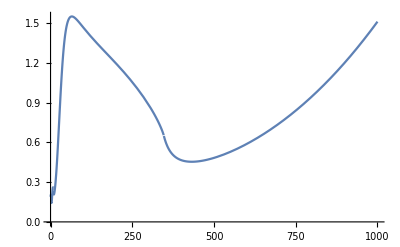

-Graphics3D-

```mathematica
Remove [ft]
Remove[F12]
Remove[Rg]
Remove[Bg]
Remove[taut]
Remove[tauW]
Remove[taub]
Remove[tauc]
Remove[tauτ]
Mu= 0.0023;
Md= 0.0048;
Ms = 0.095;
Mc = 1.275;
Mt = 173.210;
Mb  = 4.180;
σppH= 17.62;
σggH=1.529*10;
σVBFH=1.24;
v=246;
tauu[Mx_]=4*(Mu^2/(Mx)^2);
taud[Mx_]=4*(Md^2/(Mx)^2);
taus[Mx_]=4*(Ms^2/(Mx)^2);
tauc[Mx_]=4*(Mc^2/(Mx)^2);
taut[Mx_]=4*(Mt^2/(Mx)^2);
taub[Mx_] = 4*(Mb^2/(Mx)^2);
Bg[Mx_]=7;
ft[taui_]=Piecewise[{{(ArcSin[Sqrt[1/taui]])^2,taui≥1},{(-1/4)*(Log[(1+Sqrt[1-taui])/(1-Sqrt[1-taui])]-ⅈ*π)^2,taui<1}}];
F12[tau12_]= -2*tau12*(1+(1-tau12)*ft[tau12]);
Rg[Mx_]=(Abs[-Bg[Mx]+(1/2)*(F12[tauu[Mx]]+F12[taud[Mx]]+F12[taus[Mx]]+F12[tauc[Mx]]+F12[taut[Mx]]+F12[taub[Mx]])])^2/(Abs[(1/2)*(F12[tauu[Mx]]+F12[taud[Mx]]+F12[taus[Mx]]+F12[tauc[Mx]]+F12[taut[Mx]]+F12[taub[Mx]])])^2;
Plot[Rg[Mx]/100,{Mx,0,1000}]
σppX[f_,Mx_]=((v^2/f^2)*(Rg[Mx]*σggH+σVBFH)/(σggH+σVBFH))*σppH;
Plot3D[σppX[f,Mx],{f,500,3000},{Mx,0,1000}, ColorFunction->"TemperatureMap"]
```